```mathematica
f[x_]:= (-54(a+2)Cos[ x]+ x^3+23)/((b+2)-x^2)
a =2; b = 5;
```

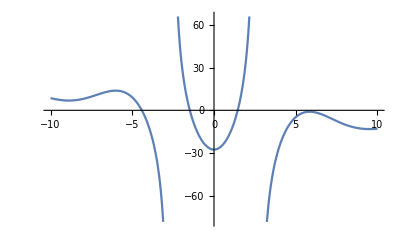

```mathematica
Plot[f[x], {x, -10,10}]
```

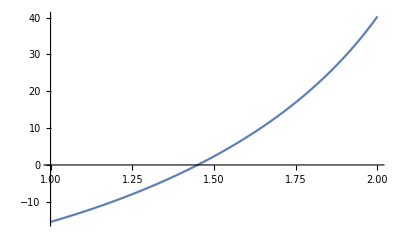

```mathematica
Plot[f[x], {x, 1,2}]
```

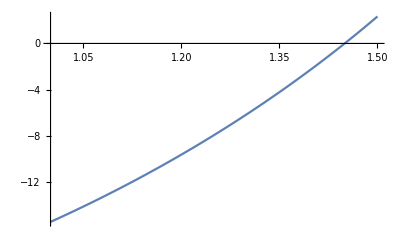

```mathematica
Plot[f[x], {x, 1,1.5}]
```

```mathematica
Plot[f[x], {x, 1,1.5}]
```

-Graphics-

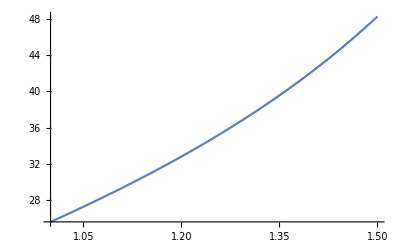

```mathematica
Plot[f'[x], {x, 1,1.5}]
(*първа производна*)
(* условието да е с посоянен знак за целия интервал е изпълнено priema samo otricatelni stoinosti *)
```

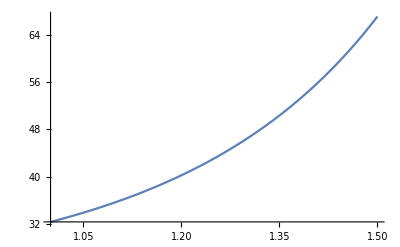

```mathematica
Plot[f''[x], {x,1,1.5}]
```

```mathematica
(*ф'' е по малко от 0 за целия и нтервал priema samo otricatelni stoinosti*)
```

```mathematica
f[1]*f[1.5]
```

-36.0925

```mathematica
(* f[1]*f[1.5]  е < 0 => има корен в интервала*)
(* всички условия на метода са изпълнени*)
```

```mathematica
(* избор за началмо приближение там където заедно със втората производна да има един и същ знак f(x)*f'' >0 *)
```

```mathematica
f[1.]
```

-15.4509

```mathematica
f[1.5]
(*ot tuk prawim izvoda f(1.5) e nasheto nachalno priblijeni, zashtoto e otricatelna kakto i f'' e otricatelna  *)
```

2.33595

```mathematica
x1= x -f[x]/f'[x](* formula za iteracii*)
```

```mathematica
(*formula za greshkata*)
eps = 10^-6
epsk = M2/(2*m1)(x1 - x)^2
(* tyrsimm M2*)
```

```mathematica
Plot[Abs[f''[x]], {x, 1,1.5}]
```

-Graphics-

```mathematica
M2=Abs[f''[1.5]]
```

67.0501

```mathematica
Plot[Abs[f'[x]], {x, 1,1.5}]
```

-Graphics-

```mathematica
m1 = Abs[f'[1.]]

x = 1.5;eps = 10^-6; M2=Abs[f''[1.5]]; m1 = Abs[f'[1.]];epsk = 1;

Print["k  = ",0," x1 = ",x," f[x] = ",f[x]," f'[x] = ",f'[x]]

For[k = 1 ,epsk > eps,k++,
x1 = x -f[x]/f'[x];(*novo priblijenie*)
epsk = M2/(2*m1)(x1- x)^2; (*greshka na novo priblijenie*)
Print["k = ",k," x1 = ",x1," f[x] = ",f[x1]," f'[x] = ",f'[x1]," epsk = ",epsk];x=x1]
```

25.6427

k  = 0 x1 = 1.5 f[x] = 2.33595 f'[x] = 48.2562

k = 1 x1 = 1.45159 f[x] = 0.0759539 f'[x] = 45.1695 epsk = 0.00306357

k = 2 x1 = 1.44991 f[x] = 0.0000856689 f'[x] = 45.0677 epsk = 3.69671×10^-6

k = 3 x1 = 1.44991 f[x] = 1.09233×10^-10 f'[x] = 45.0676 epsk = 4.72413×10^-12

```mathematica
(*2.Zadacha ////////////////////////////////*)
```

```mathematica
A=({{40+b-a, a, 0.3}, {a, -21, b}, {a+1, 2-b, 72}})
```

{{42.,2.,0.3},{2.,-21,4},{3.,-2,72}}

```mathematica
bzadacha2=({{a}, {a-b}, {b+1}})
```

{{2},{-3},{6}}

```mathematica
LinearSolve[A,bzadacha2]
```

{{0.0380967},{0.167612},{0.0887298}}

```mathematica
(*Iteratsionen procec metod na Qkobi*)
```

```mathematica
(*Forumuli
za matrisa C
Subscript[Subscript[C, i], j]=(-Subscript[Subscript[a, i], j])/Subscript[Subscript[a, i], i],i≠j=1,2,...n
Subscript[Subscript[C, i], i]=0,i=1,2,...n
za vektor d:
Subscript[d, i]=Subscript[b, i]/Subscript[a, ii],i=1,2,...n
*)
```

```mathematica
n=Length[A]
```

3

```mathematica
(*inisializasiq matrisa C i wektor d*)
```

```mathematica
c=({{□, □, □}, {□, □, □}, {□, □, □}})
```

{{□,□,□},{□,□,□},{□,□,□}}

```mathematica
d={0,0,0}
```

{0,0,0}

```mathematica
For[i=1,i≤n,i++,
c⟦i⟧=-A⟦i⟧/A⟦i,i⟧;
c⟦i,i⟧=0;
d⟦i⟧=bzadacha2⟦i⟧/A⟦i,i⟧;

]
c//MatrixForm
d//MatrixForm
```

```mathematica
({{0, -2/43, -0.0069767441860465115}, {2/21, 0, 5/21}, {-1/24, 1/24, 0}})(*glavniq diagonal zadiljitelno trabwa da e 0*)
```

(2/43
1/7
1/12)

```mathematica
(* a)*)

43 Subscript[x, 1]+2 Subscript[x, 2]+0.3 Subscript[x, 3]=2
2 Subscript[x, 1]+-21 Subscript[x, 2]+5 Subscript[x, 3]=-3
3 Subscript[x, 1]-3 Subscript[x, 2]+72 Subscript[x, 3]=6
(*za i-tiq red prehvirlqm vsichko,koeto e bez Subscript[x, i] ot dqsnata s obraten znak*)
43 Subscript[x, 1]=-2 Subscript[x, 2]-0.3 Subscript[x, 3]+2
-21 Subscript[x, 2]=-2 Subscript[x, 1]-5 Subscript[x, 3]-3
72 Subscript[x, 3]=-3 Subscript[x, 1]+3 Subscript[x, 2]+6

(*za i-tiq red delim na koefisienta pred Subscript[x, i]*)
Subscript[x, 1]^(k+1)=-2/43 Subscript[x, 2]^(k)-0.3/43 Subscript[x, 3]^(k)+2/43
Subscript[x, 2]^(k+1)=-2/-21 Subscript[x, 1]^(k)-5/-21 Subscript[x, 3]^(k)-3/-21
Subscript[x, 3]^(k+1)=-3/72 Subscript[x, 1]^(k)+3/72 Subscript[x, 2]^(k)+6/72
```

```mathematica
(*k=0,1,2..*)
```

```mathematica
(* b)proverka na shodimost *)
```

```mathematica
Norm[c]
```

0.256999

```mathematica
(*po-malka ot 1 izvoda e shte bide shodqsht *)
```

```mathematica
(* v) izbor na nachalno priblijenie*)

(*formula
x^(k+1)=C.x^(k)+d
*)
```

```mathematica
x0 = {3,6,68}(*nqma znachenie*)
Print["k = ",0, "x^(k)= ",x0]
For[k = 1,k≤5,k++,
x2 = c.x0+d;
x0=x2;
Print["k = ",k, "x^(k)= ",x0]
]
```

{3,6,68}

k = 0x^(k)= {3,6,68}

k = 1x^(k)= {{-0.706977},{16.619},{0.208333}}

k = 2x^(k)= {{-0.727921},{0.125129},{0.805251}}

k = 3x^(k)= {{0.0350736},{0.265258},{0.118877}}

k = 4x^(k)= {{0.0333447},{0.174502},{0.0929243}}

k = 5x^(k)= {{0.037747},{0.168158},{0.0892149}}

```mathematica
(*za sravnenie gore LinearSolve
{{0.0380966973576075},{0.16761153905085596},{0.08872978507055201}}
*)
```

```mathematica
(* d) otsenka na greshka*)
```

```mathematica
(*formula
e^(k)=||x^*-x^(k)||≤||C(||)^(k)(||x^(0)||+(||d||)/(1-||C||))
*)
```

```mathematica
x0 = {3,6,68}(*nqma znachenie*)
nx0 = Norm[x0];
eps1 =Norm[c]^0(nx0+Norm[d]/(1-Norm[c]));
Print["k = ",0, "x^(k)= ",x0, "e^(k)= ",eps1]
For[k = 1,k≤5,k++,
x2 = c.x0+d;
x0=x2;
eps1 = Norm[c]^k(nx0+Norm[d]/(1-Norm[c]));
Print["k = ",k, "x^(k)= ",x0, "e^(k)= ",eps1]
]
```

{3,6,68}

k = 0x^(k)= {3,6,68}e^(k)= 68.5613

k = 1x^(k)= {{-0.706977},{16.619},{0.208333}}e^(k)= 17.6202

k = 2x^(k)= {{-0.727921},{0.125129},{0.805251}}e^(k)= 4.52836

k = 3x^(k)= {{0.0350736},{0.265258},{0.118877}}e^(k)= 1.16378

k = 4x^(k)= {{0.0333447},{0.174502},{0.0929243}}e^(k)= 0.299091

k = 5x^(k)= {{0.037747},{0.168158},{0.0892149}}e^(k)= 0.0768661

```mathematica
(*Zadacha 3 ///////////////////////////////////////*)
```

```mathematica
(* a) sistavqne na tablitsata*)
(*
Subscript[x, 1]=10+b+i(0.3);i=OverBar[0,10]
*)
```

```mathematica
xt = Table[10+b+i*(0.3),{i,0,10}]
```

{15.,15.3,15.6,15.9,16.2,16.5,16.8,17.1,17.4,17.7,18.}

```mathematica
(*ot 1 zadacha*)
```

```mathematica
f[x_]:= (-54(a+2)Cos[ x]+ x^3+23)/((b+2)-x^2)
```

```mathematica
f[xt](*prilagane xt v f*)
```

{-16.3399,-16.746,-17.0679,-17.3089,-17.4793,-17.5941,-17.6724,-17.7345,-17.8013,-17.8913,-18.0201}

```mathematica
{{Subscript[x, i], 15., 15.3, □, 17.4, 17.7, 18.}, {Subscript[y, i], -16.3399, -16.746, □, -17.8013, -17.8913, -18.0201}}
```

```mathematica
Length[xt]
```

11

```mathematica
(* b) izbirane podhodqshti tochki L2*)
```

```mathematica
k= 10+b+0.25*a+0.02
```

15.52

```mathematica
(*izbirame podhodqshto cislo ot gornata tablitsa*)
```

```mathematica
{{x0, x1, x2}}
```

```mathematica
{{Subscript[x, i], 15., 15.3, 15.6}, {Subscript[y, i], -16.3399, -16.746, -17.0679}}
```

```mathematica
(* v) Postroqvane na interpotsionen polinom*)
```

```mathematica
(**formula 
L2(x)=Subscript[y, 0](((x-Subscript[x, 1])(x-Subscript[x, 2]))/((Subscript[x, 0]-Subscript[x, 1])(Subscript[x, 0]-Subscript[x, 2])))+Subscript[y, 1](((x-Subscript[x, 0])(x-Subscript[x, 2]))/((Subscript[x, 1]-Subscript[x, 0])(Subscript[x, 1]-Subscript[x, 2])))+Subscript[y, 2](((x-Subscript[x, 0])(x-Subscript[x, 1]))/((Subscript[x, 2]-Subscript[x, 0])(Subscript[x, 2]-Subscript[x, 1])))
)
```

```mathematica
L2[x_]:=-16.3399*(((x-15.3)(x-15.6))/((15.-15.3)(15.-15.6)))+-16.746*(((x-15.)(x-15.6))/((15.3-15.)(15.3-15.6)))+-17.0679*(((x-15.)(x-15.3))/((15.6-15.)(15.6-15.3)))
```

```mathematica
L2[x]
```

-90.7772 (-15.6+x) (-15.3+x)+186.067 (-15.6+x) (-15.+x)-94.8217 (-15.3+x) (-15.+x)

```mathematica
Expand[L2[x]]
```

111.32-15.5273 x+0.467778 x^2

```mathematica
(* g)Proverka dali postroeniq polinom udevlotvorqvane*)
```

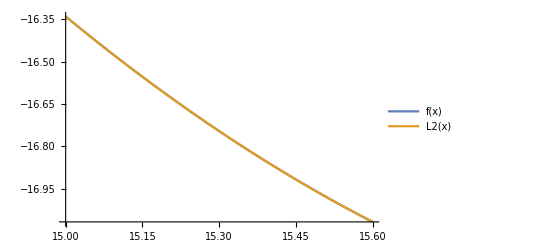

```mathematica
Plot[{f[x],L2[x]},{x,15.,15.6},PlotLegends->"Expressions"]
```

```mathematica
(*proverka dali sivpada*)
```

```mathematica
{{Subscript[x, i], 15., 15.3, 15.6}, {Subscript[y, i], -16.3399, -16.746, -17.0679}}
```

```mathematica
L2[15.]
L2[15.3]
L2[15.6]
```

-16.3399

-16.746

-17.0679

```mathematica
(* d) namirane na priblijenata stoynost na funksiata f(k)*)
```

```mathematica
k= 10+b+0.25*a+0.02
```

15.52

```mathematica
L2[15.52]
```

-16.9903

```mathematica
Print["Priblijena stoynost na funksiata = ",L2[15.52],"Tochnata stoynost na funksiata = ",f[15.52],"Istinskata greshka na priblijenieto e ",Abs[L2[15.52]-f[15.52]]]
```

Priblijena stoynost na funksiata = -16.9903Tochnata stoynost na funksiata = -16.9902Istinskata greshka na priblijenieto e 0.0000958898

```mathematica
(* e) Teoretichna otsenka na greshkata*)
(*formula
|Subscript[R, n](x)|=|f(x)-Subscript[L, n](x)|≤Subscript[M, n+1]/((n+1)!)(x-Subscript[x, 0])...(x-Subscript[x, n])
Subscript[R, 2]= za polinom ot vtora stepen
*)
```

```mathematica
Subscript[R, 2](x)≤Subscript[M, 3]/(3!)|(x-Subscript[x, 0])(x-Subscript[x, 1])(x-Subscript[x, 3])|,kideto Subscript[M, 3] = max|f'''(x)|
```

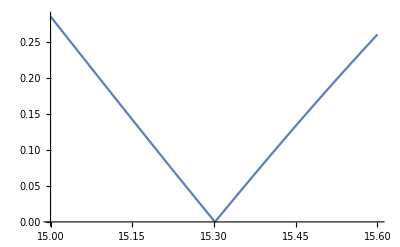

```mathematica
Plot[Abs[f'''[x]],{x,15.,15.6}]
```

```mathematica
M3 = Abs[f'''[15.6]]
```

0.261035

```mathematica
R2[x_]:=M3/(3!)Abs[(x-15.)(x-15.3)(x-15.6)]
```

```mathematica
k= 10+b+0.25*a+0.02
```

15.52

```mathematica
R2[15.52]
```

0.000398166

```mathematica
(*za sravnenie*)
```

```mathematica
"Istinskata greshka na priblijenieto e "0.0000958898
```

```mathematica
(*v sluchay na ekstrapolatsia*)
```

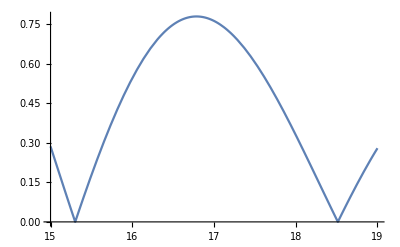

```mathematica
Plot[Abs[f'''[x]],{x,15.,19}]
```

```mathematica
M3=0.8
```

```mathematica
R2[x_]:=M3/(3!)Abs[(x-15.)(x-15.3)(x-15.6)]
```

```mathematica
R2[0.8]
```

132.576

```mathematica
(* j) Postroqvame polinom na lineyna regresia*)

xt
```

{15.,15.3,15.6,15.9,16.2,16.5,16.8,17.1,17.4,17.7,18.}

```mathematica
yt=f[xt]
```

{-16.3399,-16.746,-17.0679,-17.3089,-17.4793,-17.5941,-17.6724,-17.7345,-17.8013,-17.8913,-18.0201}

```mathematica
xt^2
```

{225.,234.09,243.36,252.81,262.44,272.25,282.24,292.41,302.76,313.29,324.}

```mathematica
xt*yt
```

{-245.098,-256.214,-266.259,-275.212,-283.164,-290.303,-296.896,-303.261,-309.742,-316.675,-324.362}

```mathematica
Np = Length[xt]
```

11

```mathematica
∑_(i=1)^Np xt[[i]]
```

181.5

```mathematica
∑_(i=1)^Np yt[[i]]
```

-191.656

```mathematica
∑_(i=1)^Np xt[[i]]^2
```

3004.65

```mathematica
∑_(i=1)^Np xt[[i]]yt[[i]]
```

-3167.19

```mathematica
11 Subscript[a, 0]+181.5 Subscript[a, 1]=-191.656
```

```mathematica
181.5 Subscript[a, 0]+3004.65=-3167.19
```

```mathematica
Azadacha3=({{11, 181.5}, {181.5, 3004.65}});
bzadacha3={-191.656,-3167.19};
```

```mathematica
LinearSolve[Azadacha3,bzadacha3]
```

{-9.31327,-0.491515}

```mathematica
P1[x_]:=-0.491515x+-9.31327
```

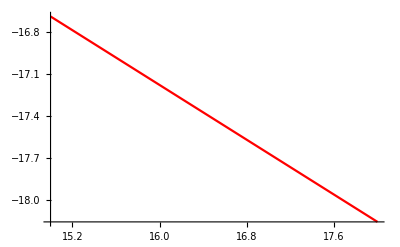

```mathematica
grP1 = Plot[P1[x],{x,xt[[1]],xt[[Np]]},PlotStyle->Red]
```

```mathematica
greshka=√(∑_(i=1)^Np (yt ⟦i⟧- P1[xt⟦i⟧])^2)
```

0.536198

```mathematica
(*lineyna regresia ot vtora stepen*)
```

```mathematica
xt^3
```

{3375.,3581.58,3796.42,4019.68,4251.53,4492.13,4741.63,5000.21,5268.02,5545.23,5832.}

```mathematica
xt^4
```

{50625.,54798.1,59224.1,63912.9,68874.8,74120.1,79659.4,85503.6,91663.6,98150.6,104976.}

```mathematica
xt^2*yt
```

{-3676.47,-3920.07,-4153.63,-4375.87,-4587.26,-4790.,-4987.85,-5185.76,-5389.51,-5605.15,-5838.51}

```mathematica
∑_(i=1)^Np xt⟦i⟧^3
```

49903.4

```mathematica
∑_(i=1)^Np xt⟦i⟧^4
```

831508.

```mathematica
∑_(i=1)^Np xt⟦i⟧^2 yt⟦i⟧
```

-52510.1

```mathematica
Azadacha3.1=({{11, 181.5, 3004.65}, {181.5, 3004.65, 49903.4}, {3004.65, 49903.4, 831508.}});
bzadacha3.1={-191.656,-3167.19,-52510.1};
```

```mathematica
LinearSolve[Azadacha3.1,bzadacha3.1]
```

{-9.31327,-0.491515}

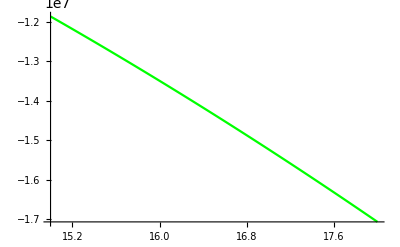

```mathematica
P2[x_]:=-52510.1 x^2-3167.19x+-191.656

grP2= Plot[P2[x],{x,xt[[1]],xt[[Np]]},PlotStyle->Green]
```

```mathematica
greshkazad3=√(∑_(i=1)^Np (yt ⟦i⟧- P2[xt⟦i⟧])^2)
```

4.80563×10^7

```mathematica
(* y) presmetnete∫_a^(a+b+1) *)
```

```mathematica
∫_2^(2+5+1) Cos[x]ⅆx
```

-Sin[2]+Sin[8]

```mathematica
%// N
```

0.0800608

```mathematica
∫_2.^8 (Cos[x])^2/(x^3+ⅇ^(x^2))ⅆx
```

∫_2.^8 Cos[x]^2/(ⅇ^(x^2)+x^3)ⅆx

```mathematica
NIntegrate[(2345 Cos[x]^2)/(ⅇ^(x^2)+x^3),{x,2.,8}]
```

3.25017

```mathematica
(*formula na levite ∑_(i=0)^(n-1) h*f(x^i)*)
```

```mathematica
a=2.;b=5;
n=3;h=(b-a)/n;
mrezha = Table[a+i*h,{i,0,n}];
f[x_]:=(2345 Cos[x]^2)/(ⅇ^(x^2)+x^3)
Itochno = NIntegrate[(2345 Cos[x]^2)/(ⅇ^(x^2)+x^3),{x,2.,8}];
I1 = ∑_(i=0)^(n-1) h*f[a+i*h];
Print["Точната стойност на интеграла е I_(:0442:043e:0447:043d:043e:0441:0442) = ",Itochno]
Print["Приближената стойност на интеграла по формула на левите правоъг. е I_1 = ",I1]
Print["Точната грешка на приближението е I_(:0442:043e:0447:043d:043e:0441:0442)-I_1 = ",Abs[Itochno - I1]]
```

Точната стойност на интеграла е I_точност = 3.25017

Приближената стойност на интеграла по формула на левите правоъг. е I_1 = 6.77026

Точната грешка на приближението е I_точност-I_1 = 3.52009

```mathematica
(*4.Zadacha*)
```

```mathematica
(*
	y'=y-1n(x^2+1)+(2x)/(x^2+1)
y(a)=b 
x ϵ |a,a+2| 
*)

Clear[x,y,f]
```

```mathematica
DSolve[{y'[x]==y[x]-1n(x^2+1)+(2x)/x^2+1,y[2]==5},y,x]
```

{{y→Function[{x},-1/ⅇ^2(ⅇ^2-6 ⅇ^x-3 ⅇ^2 n+11 ⅇ^x n-2 ⅇ^2 n x-ⅇ^2 n x^2+2 ⅇ^(2+x) ExpIntegralEi[-2]-2 ⅇ^(2+x) ExpIntegralEi[-x])]}}

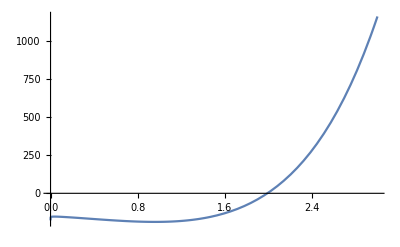

```mathematica
yex[x_]:=-1/ⅇ^2(ⅇ^2-6 ⅇ^x-3 ⅇ^2 n+11 ⅇ^x n-2 ⅇ^2 n x-ⅇ^2 n x^2+2 ⅇ^(2+x) ExpIntegralEi[-2]-2 ⅇ^(2+x) ExpIntegralEi[-x])
Plot[yex[x],{x,0,3}]
```

```mathematica
a=2;b=4;
```

```mathematica
h=0.02;
n=b-a/h;
y0=5;
```

```mathematica
f[x_,y_]:=y-1n(x^2+1)+(2x)/(x^2+1)
```

```mathematica
f[2,0]
```

480.8

```mathematica
%//N
```

480.8

```mathematica
yex[2]
```

5.